```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
```

## Parameters

```mathematica
(*Approximations: complexes are in equilibrium, effectors are conserved.

 r+e <-->e+a
t+e --> (te)b-->e

*)
```

```mathematica
gT=10; (*t growth*)
gR=1; (*NLR growth*)
deltaT=1; (*t decay*)
deltaR=1; (*NLR decay*)
beta1=1; (*effector-target affinity*)
beta2=1; (*effector-target unbinding*)
```

```mathematica
alphaF=0.5; (*R-T complex formation*)
alphaB=1; (*R-T complex unbinding*)
gamma1=1;  (*complex-effector binding*)
gamma2=5; (*complex-effector unbinding*)
```

```mathematica
e0=3; (*total effector concentration*)
```

## Equations

```mathematica
(*solve for E based on e0 and quasi-equilibrium*)
```

```mathematica
fixedEEq=x+(beta1/beta2)*tVar*x+(gamma1/gamma2)*rVar*x-e0Var==0;
fixedSol=x/.Solve[fixedEEq,x];
getE[thisR_?NumericQ,thisT_?NumericQ,thisE0_?NumericQ]:=Module[{numericSol,final},

numericSol=fixedSol/.{rVar->thisR,tVar->thisT,e0Var->thisE0}//N;

If[numericSol[[1]]>0,final=numericSol[[1]],final="error"];
final
]
```

```mathematica
drds[rVar_,tVar_,aVar_,e0Var_]:=Module[{thisE,thisZ},

thisE=getE[rVar,tVar,e0Var];
gR-deltaR*rVar-rVar*gamma1*thisE+f[aVar]
]
```

```mathematica
dtds[rVar_,tVar_,e0Var_]:=Module[{thisE,thisZ},
thisE=getE[rVar,tVar,e0Var];
gT-deltaT*tVar-beta1*tVar*thisE
]
```

```mathematica
dads[rVar_,tVar_,aVar_,e0Var_]:=Module[{thisE,thisZ},

thisE=getE[rVar,tVar,e0Var];
rVar*gamma1*thisE-deltaR*aVar
]
(*dads=r[s]*t[s]*e*z;*)
```

```mathematica
f[z_]:=z^2;(*feedback*)
```

## solver

```mathematica
(* remove duplicates *)
processRoots[rootList_]:=Module[{cleanList,test,unique,thisDist,i,j},
cleanList={rootList[[1]]};
For[i=2,i<=Length[rootList],i++,

test=rootList[[i]];
unique=True;
For[j=1,j<=Length[cleanList],j++,
	thisDist=EuclideanDistance[test,cleanList[[j]]];
	If[thisDist<10^-5,unique=False];
];
If[unique==True,AppendTo[cleanList,test];];

];

cleanList
]
```

```mathematica
getFixedPoint[e0Var_]:=Module[{rootList,thisSol,thisGuess,guessList,cleanList,i,j,k},

guessList={0.1,1,10,100};
rootList={};
Print[e0Var];
For[i=1,i<=Length[guessList],i++,
For[j=1,j<=Length[guessList],j++,
For[k=1,k<=Length[guessList],k++,

thisSol=FindRoot[{drds[rVar,tVar,aVar,e0Var]==0,dtds[rVar,tVar,e0Var]==0,dads[rVar,tVar,aVar,e0Var]==0},{rVar,guessList[[i]],0,10^6},{tVar,guessList[[j]],0,10^6},{aVar,guessList[[k]],0,10^6}];
residual=(drds[rVar,tVar,aVar,e0Var])^2+(dtds[rVar,tVar,e0Var])^2+(dads[rVar,tVar,aVar,e0Var])^2/.thisSol; (*check convergence*)
If[residual<=10^-6,AppendTo[rootList,{rVar,tVar,aVar}/.thisSol];];
];
];
];
cleanList=processRoots[rootList];
cleanList
]
```

```mathematica
e0List=Join[{0.001},Range[0.5,2.5,.5],Range[3,5,.1],Range[5.5,20,0.5]];
```

```mathematica
(*(e,list of fixed points)*)
fixedPointList=Table[{i,getFixedPoint[i]},{i,0,20,.1}];
```

0.

FindRoot::nlnum: The function value {0.91-0.1 error,9.9-0.1 error,-0.1+0.1 error} is not a list of numbers with dimensions {3} at {rVar,tVar,aVar} = {0.1,0.1,0.1}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[{drds[rVar,tVar,aVar,0.]==0,dtds[rVar,tVar,0.]==0,dads[rVar,tVar,aVar,0.]==0},{rVar,guessList$6133785⟦i$6133785⟧,0,10^6},{tVar,guessList$6133785⟦j$6133785⟧,0,10^6},{aVar,guessList$6133785⟦k$6133785⟧,0,10^6}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

0.1

FindRoot::reged: The point {0.,8.52896,5.61066} is at the edge of the search region {0.,1.×10^6} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {0.,10.1107,43.8701} is at the edge of the search region {0.,1.×10^6} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {0.,1.00013,9.99441} is at the edge of the search region {0.,1.×10^6} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

0.2

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

0.3

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.4

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

0.5

0.6

0.7

0.8

0.9

1.

1.1

1.2

1.3

1.4

1.5

1.6

1.7

1.8

1.9

2.

2.1

2.2

2.3

2.4

2.5

2.6

2.7

2.8

2.9

3.

3.1

3.2

3.3

3.4

3.5

3.6

3.7

3.8

3.9

4.

4.1

4.2

4.3

4.4

4.5

4.6

4.7

4.8

4.9

5.

5.1

5.2

5.3

5.4

5.5

5.6

5.7

5.8

5.9

6.

6.1

6.2

6.3

6.4

6.5

6.6

6.7

6.8

6.9

7.

7.1

7.2

7.3

7.4

7.5

7.6

7.7

7.8

7.9

8.

8.1

8.2

8.3

8.4

8.5

8.6

8.7

8.8

8.9

9.

9.1

9.2

9.3

9.4

9.5

9.6

9.7

9.8

9.9

10.

10.1

10.2

10.3

10.4

10.5

10.6

10.7

10.8

10.9

11.

11.1

11.2

11.3

11.4

11.5

11.6

11.7

11.8

11.9

12.

12.1

12.2

12.3

12.4

12.5

12.6

12.7

12.8

12.9

13.

13.1

13.2

13.3

13.4

13.5

13.6

13.7

13.8

13.9

14.

14.1

14.2

14.3

14.4

14.5

14.6

14.7

14.8

14.9

15.

15.1

15.2

15.3

15.4

15.5

15.6

15.7

15.8

15.9

16.

16.1

16.2

16.3

16.4

16.5

16.6

16.7

16.8

16.9

17.

17.1

17.2

17.3

17.4

17.5

17.6

17.7

17.8

17.9

18.

18.1

18.2

18.3

18.4

18.5

18.6

18.7

18.8

18.9

19.

19.1

19.2

19.3

19.4

19.5

19.6

19.7

19.8

19.9

20.

```mathematica
(*convert a list where each e has a 3D ss, to coordinates for plotting. want r*(e), t*(e), a*(e)*)
getPlottingCoords[fixedPoints_]:=Module[{},

rPoints={};
tPoints={};
aPoints={};

For[i=1,i<=Length[fixedPoints],i++,

thisPoint=fixedPoints[[i]];
eValue=thisPoint[[1]];

For[j=1,j<=Length[thisPoint[[2]]],j++,

thisFixedPoint=thisPoint[[2,j]];
AppendTo[rPoints,{eValue,thisFixedPoint[[1]]}];
AppendTo[tPoints,{eValue,thisFixedPoint[[2]]}];
AppendTo[aPoints,{eValue,thisFixedPoint[[3]]}];
];
];

{rPoints,tPoints,aPoints}

]
```

```mathematica
{rCoords,tCoords,aCoords}=getPlottingCoords[fixedPointList];
```

Part::partw: Part 3 of {}⟦1⟧ does not exist.

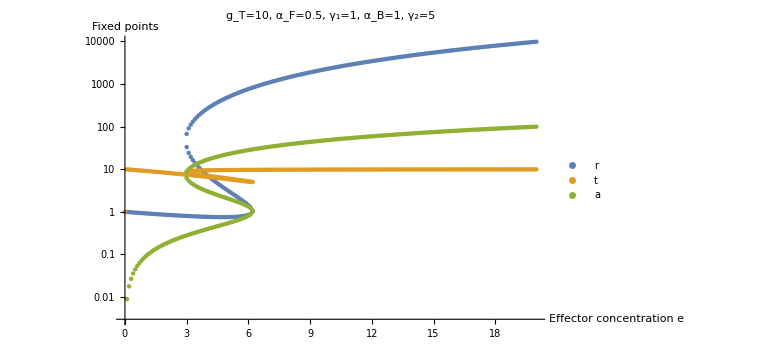

```mathematica
plot=ListLogPlot[{rCoords,tCoords,aCoords},PlotRange->{Automatic,Automatic},PlotLabel->"g_T="<>ToString[gT]<>", α_F="<>ToString[alphaF]<>", γ_1="<>ToString[gamma1]<>", α_B="<>ToString[alphaB]<>", γ_2="<>ToString[gamma2],AxesLabel->{"Effector concentration e","Fixed points"},LabelStyle->Directive[Black, 10],PlotLegends->{"r","t","a"},ImageSize->Large]
```

```mathematica
Export["directRecognitionPoints_rta.mx",{rCoords,tCoords,aCoords}]
```

directRecognitionPoints_rta.mx

## fixed point complex formation

```mathematica
getBoundTarget[rVar_,tVar_,e0Var_]:=(beta1/beta2)*tVar*getE[rVar,tVar,e0Var];
```

```mathematica
(*given fixed points for r, t, a, compute E, complex, (te)^b,(Ce)^b, *)
(*output=(E0,((E1, complex1,boundTarget1,boundComplex1),(E2, complex2,boundTarget2,boundComplex2)...)*)
convertPoints[inputFixedPoints_]:=Module[{thisE0,pointList,thisBindingList,i,thisR,thisT,thisA,thisE,thisComplex,thisBoundComplex,thisBoundTarget,thisPoint,output},

thisE0=inputFixedPoints[[1]];
pointList=inputFixedPoints[[2]];
(*a list containing a list for each fixed point*)
thisBindingList={};
For[i=1,i<=Length[pointList],i++,

{thisR,thisT,thisA}=pointList[[i]];
thisE=getE[thisR,thisT,thisE0];

thisBoundTarget=getBoundTarget[thisR,thisT,thisE0];


thisPoint={thisE,thisBoundTarget};

AppendTo[thisBindingList,thisPoint];
];

output={thisE0,thisBindingList}

]
```

```mathematica
(*convert a list where each e has a 3D ss, to coordinates for plotting. want r*(e), t*(e), a*(e)*)
getBoundPlottingCoords[boundPoints_]:=Module[{i,j,ePoints,complexPoints,boundTargetPoints,boundComplexPoints,thisPoint,eValue,thisFixedPoint},

ePoints={};
complexPoints={};
boundTargetPoints={};
boundComplexPoints={};

For[i=1,i<=Length[boundPoints],i++,

thisPoint=boundPoints[[i]];
eValue=thisPoint[[1]];

For[j=1,j<=Length[thisPoint[[2]]],j++,

thisFixedPoint=thisPoint[[2,j]];
AppendTo[ePoints,{eValue,thisFixedPoint[[1]]}];
AppendTo[boundTargetPoints,{eValue,thisFixedPoint[[2]]}];

];
];

{ePoints,complexPoints,boundTargetPoints,boundComplexPoints}

]
```

```mathematica
(*calculate complexes from fixed points*)
```

```mathematica
allBoundFixedPoints=Table[convertPoints[fixedPointList[[i]]],{i,Length[fixedPointList]}];
```

Set::shape: Lists {thisR$10025150,thisT$10025150,thisA$10025150} and {}⟦1⟧ are not the same shape.

```mathematica
(*convert to coordinates for plotting*)
{eCoords,boundTargetCoords}=getBoundPlottingCoords[allBoundFixedPoints];
```

Set::shape: Lists {eCoords,boundTargetCoords} and {{{0.,getE[thisR$10025150,thisT$10025150,0.]},{0.1,0.0090017},{0.2,0.0181518},{0.3,0.0274534},{0.4,0.03691},{0.5,0.046525},{0.6,0.0563017},{0.7,0.0662438},{0.8,0.076355},{0.9,0.086639},«257»},{},{{0.,thisT$10025150 getE[thisR$10025150,thisT$10025150,0.]},{0.1,0.0892139},{0.2,0.178281},«5»,{0.8,0.709385},{0.9,0.797312},«257»},{}} are not the same shape.

```mathematica
(*plot*)
```

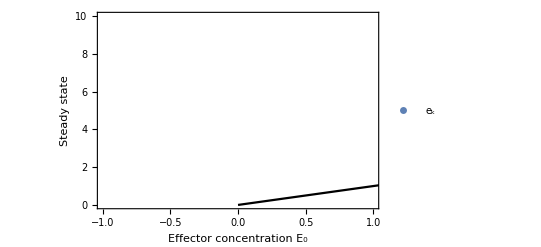

```mathematica
Show[ListPlot[{eCoords,boundTargetCoords},PlotRange->{Automatic,{0,10}},Frame->{True,True,False,False},FrameLabel->{"Effector concentration E_0","Steady state"},LabelStyle->Directive[Black, 12],PlotLegends->{"e_k","(t_je_k)^b"}],Plot[x,{x,0,6},PlotStyle->Black]]
```